```mathematica
f[u_]:= a Cos[u]
```

```mathematica
g[u_]:= ∫_0^u √(1-a^2 Sin[t]^2)ⅆt
```

```mathematica
g[u]
```

$Aborted

```mathematica
∫√(1-a^2 Sin[t]^2)ⅆt
```

EllipticE[t,a^2]

```mathematica
g[u_]:= EllipticE[u,a^2]
```

```mathematica
a=1/2
```

1/2

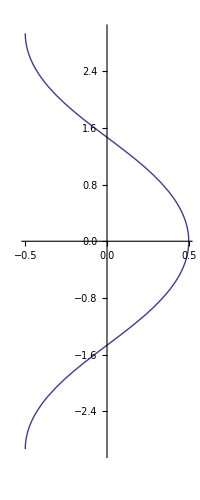

```mathematica
ParametricPlot[{f[u],g[u]},{u,-π,π}]
```

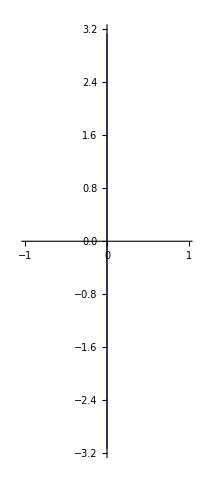
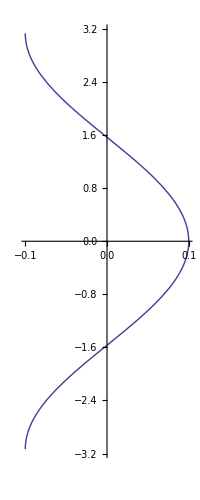
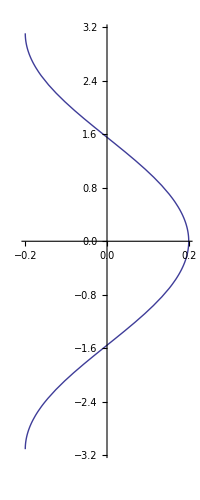
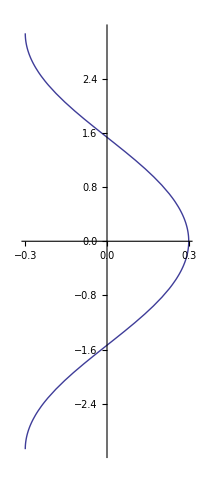
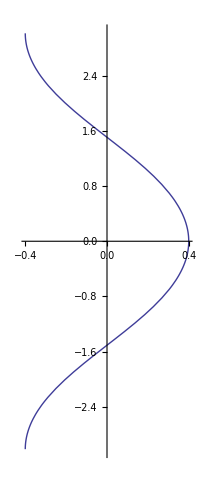
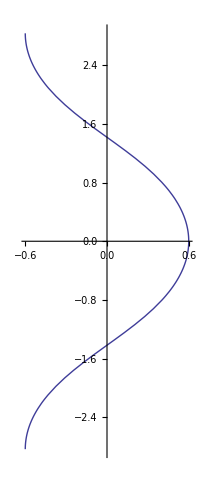
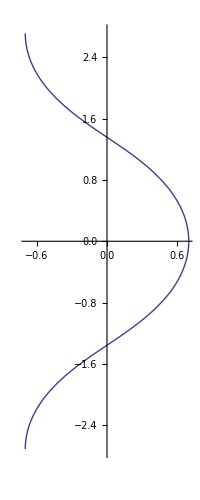
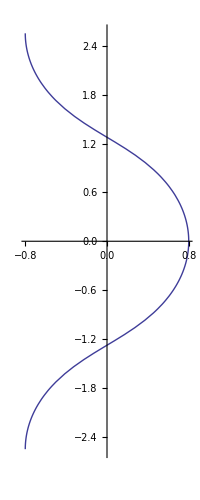
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ParametricPlot[{f[u],g[u]},{u,-π,π}],{a,0,2,.1}]
```

```mathematica
Table[ParametricPlot3D[{f[u]Cos[t], f[u]Sin[t],g[u]},{u,-π,π},{t,0,2π}],{a,0,2,.1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}